```mathematica
K1=720;
K2=720;
K3=0.007;
K4=0.007;
daSYN=15;
kaSYN=8.5;
(*S1=0.0*)
(*S2=1;*)
S3=1;
S4=1;
```

```mathematica
f[ROS_,S1_,S2_]:=K1*(1+S1+daSYN*((K3*ROS*S3/(kaSYN*K4*S4))^4)/(1+(K3*ROS*S3/(kaSYN*K4*S4))^4)) -(K2*ROS*S2)
```

```mathematica
fps=Solve[f[ROS, S1, S2]==0, ROS]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{ROS→Root[-83521-83521 S1+83521 S2 #1+(-256-16 S1) #1^4+16 S2 #1^5&,1]},{ROS→Root[-83521-83521 S1+83521 S2 #1+(-256-16 S1) #1^4+16 S2 #1^5&,2]},{ROS→Root[-83521-83521 S1+83521 S2 #1+(-256-16 S1) #1^4+16 S2 #1^5&,3]},{ROS→Root[-83521-83521 S1+83521 S2 #1+(-256-16 S1) #1^4+16 S2 #1^5&,4]},{ROS→Root[-83521-83521 S1+83521 S2 #1+(-256-16 S1) #1^4+16 S2 #1^5&,5]}}

```mathematica
Solve[(ROS/.fps[[2]])==(ROS/.fps[[3]]),S1]
```

Solve::ivar: 0. is not a valid variable.

Solve[False,0.]

```mathematica
bifSol=Solve[{f[ROS, S1, S2]==0, D[f[ROS, S1, S2]==0, ROS]},{S1, S2}]
```

{{S1→-(16. (1.70307×10^6-14028.9 ROS^4+1. ROS^8))/((5220.06+1. ROS^4)^2),S2→-(2.20191×10^-6 ROS^7)/((1.+0.000191569 ROS^4)^2)+(0.0114941 ROS^3)/(1.+0.000191569 ROS^4)}}

```mathematica
bifSol[[1]]
```

{S1→-(16. (1.70307×10^6-14028.9 ROS^4+1. ROS^8))/((5220.06+1. ROS^4)^2),S2→-(2.20191×10^-6 ROS^7)/((1.+0.000191569 ROS^4)^2)+(0.0114941 ROS^3)/(1.+0.000191569 ROS^4)}

```mathematica
{S1, S2}/.bifSol[[1]]
```

{-(16. (1.70307×10^6-14028.9 ROS^4+1. ROS^8))/((5220.06+1. ROS^4)^2),-(2.20191×10^-6 ROS^7)/((1.+0.000191569 ROS^4)^2)+(0.0114941 ROS^3)/(1.+0.000191569 ROS^4)}

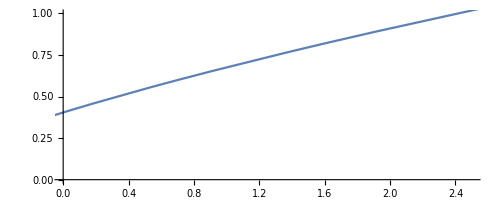

```mathematica
ParametricPlot[{S1, S2}/.bifSol[[1]],{ROS,-10,40},PlotRange->{{0,2.5},{0,1}}]
```

```mathematica
K1=720;
K2=720;
K3=0.007;
K4=0.007;
daSYN=15;
kaSYN=8.5;
S1=0.0
(*S2=1;
S3=1;*)
S4=1;
```

0.

```mathematica
g[ROS_,S1_,S3_]:=K1*(1+S1+daSYN*((K3*ROS*S3/(kaSYN*K4*S4))^4)/(1+(K3*ROS*S3/(kaSYN*K4*S4))^4)) -(K2*ROS*S2)
```

```mathematica
fps=Solve[g[ROS, S2, S3]==0, ROS]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{ROS→-3.93139-5.21411 ⅈ},{ROS→-3.93139+5.21411 ⅈ},{ROS→1.00291},{ROS→8.5},{ROS→14.3599}}

```mathematica
bifSol=Solve[{g[ROS, S1, S3]==0, D[g[ROS, S1, S3]==0, ROS]},{S1, S3}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{S1→9.45112×10^-16 (-1.05808×10^15+7.93557×10^14 ROS-(7.93557×10^15 ROS^7)/(ROS^7-1.76346×10^13 ROS^8)+(1.39941×10^29 ROS^8)/(ROS^7-1.76346×10^13 ROS^8)-(4.66469×10^27 ROS^9)/(ROS^7-1.76346×10^13 ROS^8)+(6.29904×10^7 ROS^4 √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(ROS^7-1.76346×10^13 ROS^8)-(1.11081×10^21 ROS^5 √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(ROS^7-1.76346×10^13 ROS^8)),S3→-17. ((3.30649×10^13 ROS^3)/(-1. ROS^7+1.76346×10^13 ROS^8)-(1.10216×10^12 ROS^4)/(-1. ROS^7+1.76346×10^13 ROS^8)-(262460. √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(-1. ROS^7+1.76346×10^13 ROS^8))^(1/4)},{S1→9.45112×10^-16 (-1.05808×10^15+7.93557×10^14 ROS-(7.93557×10^15 ROS^7)/(ROS^7-1.76346×10^13 ROS^8)+(1.39941×10^29 ROS^8)/(ROS^7-1.76346×10^13 ROS^8)-(4.66469×10^27 ROS^9)/(ROS^7-1.76346×10^13 ROS^8)+(6.29904×10^7 ROS^4 √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(ROS^7-1.76346×10^13 ROS^8)-(1.11081×10^21 ROS^5 √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(ROS^7-1.76346×10^13 ROS^8)),S3→(0.-17. ⅈ) ((3.30649×10^13 ROS^3)/(-1. ROS^7+1.76346×10^13 ROS^8)-(1.10216×10^12 ROS^4)/(-1. ROS^7+1.76346×10^13 ROS^8)-(262460. √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(-1. ROS^7+1.76346×10^13 ROS^8))^(1/4)},{S1→9.45112×10^-16 (-1.05808×10^15+7.93557×10^14 ROS-(7.93557×10^15 ROS^7)/(ROS^7-1.76346×10^13 ROS^8)+(1.39941×10^29 ROS^8)/(ROS^7-1.76346×10^13 ROS^8)-(4.66469×10^27 ROS^9)/(ROS^7-1.76346×10^13 ROS^8)+(6.29904×10^7 ROS^4 √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(ROS^7-1.76346×10^13 ROS^8)-(1.11081×10^21 ROS^5 √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(ROS^7-1.76346×10^13 ROS^8)),S3→(0.+17. ⅈ) ((3.30649×10^13 ROS^3)/(-1. ROS^7+1.76346×10^13 ROS^8)-(1.10216×10^12 ROS^4)/(-1. ROS^7+1.76346×10^13 ROS^8)-(262460. √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(-1. ROS^7+1.76346×10^13 ROS^8))^(1/4)},{S1→9.45112×10^-16 (-1.05808×10^15+7.93557×10^14 ROS-(7.93557×10^15 ROS^7)/(ROS^7-1.76346×10^13 ROS^8)+(1.39941×10^29 ROS^8)/(ROS^7-1.76346×10^13 ROS^8)-(4.66469×10^27 ROS^9)/(ROS^7-1.76346×10^13 ROS^8)+(6.29904×10^7 ROS^4 √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(ROS^7-1.76346×10^13 ROS^8)-(1.11081×10^21 ROS^5 √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(ROS^7-1.76346×10^13 ROS^8)),S3→17. ((3.30649×10^13 ROS^3)/(-1. ROS^7+1.76346×10^13 ROS^8)-(1.10216×10^12 ROS^4)/(-1. ROS^7+1.76346×10^13 ROS^8)-(262460. √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(-1. ROS^7+1.76346×10^13 ROS^8))^(1/4)},{S1→9.45112×10^-16 (-1.05808×10^15+7.93557×10^14 ROS-(7.93557×10^15 ROS^7)/(ROS^7-1.76346×10^13 ROS^8)+(1.39941×10^29 ROS^8)/(ROS^7-1.76346×10^13 ROS^8)-(4.66469×10^27 ROS^9)/(ROS^7-1.76346×10^13 ROS^8)-(6.29904×10^7 ROS^4 √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(ROS^7-1.76346×10^13 ROS^8)+(1.11081×10^21 ROS^5 √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(ROS^7-1.76346×10^13 ROS^8)),S3→-17. ((3.30649×10^13 ROS^3)/(-1. ROS^7+1.76346×10^13 ROS^8)-(1.10216×10^12 ROS^4)/(-1. ROS^7+1.76346×10^13 ROS^8)+(262460. √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(-1. ROS^7+1.76346×10^13 ROS^8))^(1/4)},{S1→9.45112×10^-16 (-1.05808×10^15+7.93557×10^14 ROS-(7.93557×10^15 ROS^7)/(ROS^7-1.76346×10^13 ROS^8)+(1.39941×10^29 ROS^8)/(ROS^7-1.76346×10^13 ROS^8)-(4.66469×10^27 ROS^9)/(ROS^7-1.76346×10^13 ROS^8)-(6.29904×10^7 ROS^4 √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(ROS^7-1.76346×10^13 ROS^8)+(1.11081×10^21 ROS^5 √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(ROS^7-1.76346×10^13 ROS^8)),S3→(0.-17. ⅈ) ((3.30649×10^13 ROS^3)/(-1. ROS^7+1.76346×10^13 ROS^8)-(1.10216×10^12 ROS^4)/(-1. ROS^7+1.76346×10^13 ROS^8)+(262460. √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(-1. ROS^7+1.76346×10^13 ROS^8))^(1/4)},{S1→9.45112×10^-16 (-1.05808×10^15+7.93557×10^14 ROS-(7.93557×10^15 ROS^7)/(ROS^7-1.76346×10^13 ROS^8)+(1.39941×10^29 ROS^8)/(ROS^7-1.76346×10^13 ROS^8)-(4.66469×10^27 ROS^9)/(ROS^7-1.76346×10^13 ROS^8)-(6.29904×10^7 ROS^4 √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(ROS^7-1.76346×10^13 ROS^8)+(1.11081×10^21 ROS^5 √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(ROS^7-1.76346×10^13 ROS^8)),S3→(0.+17. ⅈ) ((3.30649×10^13 ROS^3)/(-1. ROS^7+1.76346×10^13 ROS^8)-(1.10216×10^12 ROS^4)/(-1. ROS^7+1.76346×10^13 ROS^8)+(262460. √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(-1. ROS^7+1.76346×10^13 ROS^8))^(1/4)},{S1→9.45112×10^-16 (-1.05808×10^15+7.93557×10^14 ROS-(7.93557×10^15 ROS^7)/(ROS^7-1.76346×10^13 ROS^8)+(1.39941×10^29 ROS^8)/(ROS^7-1.76346×10^13 ROS^8)-(4.66469×10^27 ROS^9)/(ROS^7-1.76346×10^13 ROS^8)-(6.29904×10^7 ROS^4 √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(ROS^7-1.76346×10^13 ROS^8)+(1.11081×10^21 ROS^5 √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(ROS^7-1.76346×10^13 ROS^8)),S3→17. ((3.30649×10^13 ROS^3)/(-1. ROS^7+1.76346×10^13 ROS^8)-(1.10216×10^12 ROS^4)/(-1. ROS^7+1.76346×10^13 ROS^8)+(262460. √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(-1. ROS^7+1.76346×10^13 ROS^8))^(1/4)}}

```mathematica
bifSol[[1]]
```

{S1→9.45112×10^-16 (-1.05808×10^15+7.93557×10^14 ROS-(7.93557×10^15 ROS^7)/(ROS^7-1.76346×10^13 ROS^8)+(1.39941×10^29 ROS^8)/(ROS^7-1.76346×10^13 ROS^8)-(4.66469×10^27 ROS^9)/(ROS^7-1.76346×10^13 ROS^8)+(6.29904×10^7 ROS^4 √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(ROS^7-1.76346×10^13 ROS^8)-(1.11081×10^21 ROS^5 √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(ROS^7-1.76346×10^13 ROS^8)),S3→-17. ((3.30649×10^13 ROS^3)/(-1. ROS^7+1.76346×10^13 ROS^8)-(1.10216×10^12 ROS^4)/(-1. ROS^7+1.76346×10^13 ROS^8)-(262460. √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(-1. ROS^7+1.76346×10^13 ROS^8))^(1/4)}

```mathematica
{S1, S3}/.bifSol[[1]]
```

{9.45112×10^-16 (-1.05808×10^15+7.93557×10^14 ROS-(7.93557×10^15 ROS^7)/(ROS^7-1.76346×10^13 ROS^8)+(1.39941×10^29 ROS^8)/(ROS^7-1.76346×10^13 ROS^8)-(4.66469×10^27 ROS^9)/(ROS^7-1.76346×10^13 ROS^8)+(6.29904×10^7 ROS^4 √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(ROS^7-1.76346×10^13 ROS^8)-(1.11081×10^21 ROS^5 √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(ROS^7-1.76346×10^13 ROS^8)),-17. ((3.30649×10^13 ROS^3)/(-1. ROS^7+1.76346×10^13 ROS^8)-(1.10216×10^12 ROS^4)/(-1. ROS^7+1.76346×10^13 ROS^8)-(262460. √(-1. ROS^6 (-1.58711×10^16+1.05808×10^15 ROS)))/(-1. ROS^7+1.76346×10^13 ROS^8))^(1/4)}

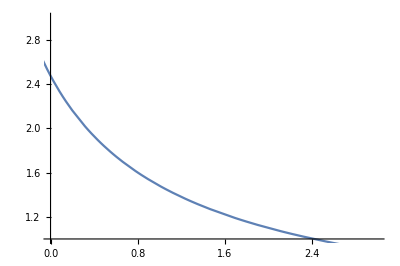

```mathematica
ParametricPlot[{S1, S3}/.bifSol[[4]],{ROS,-60,60},PlotRange->{{0,3},{1,3}}]
```